# Mathematica Notes

## Visualization and reporting

Dr. Liu Haohui

## Handy library

## Markers

```mathematica
others={-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-};
```

## Useful styling

```mathematica
Style[Rotate[#,15Degree],Bold,13]&
```

## Useful color schemes

### Sequential

Sequential schemes are suited to ordered data that progress from low to high. Lightness steps dominate the look of these schemes, with light colors for low data values to dark colors for high data values.

### Diverging

Diverging schemes put equal emphasis on mid-range critical values and extremes at both ends of the data range. The critical class or break in the middle of the legend is emphasized with light colors and low and high extremes are emphasized with dark colors that have contrasting hues.

### Qualitative

Qualitative schemes do not imply magnitude differences between legend classes, and hues are used to create the primary visual differences between classes. Qualitative schemes are best suited to representing nominal or categorical data.

```mathematica
RGBColor/@{"#7fc97f","#beaed4","#fdc086","#ffff99","#386cb0"}
```

{RGBColor[0.4980392156862745, 0.788235294117647, 0.4980392156862745],RGBColor[0.7450980392156863, 0.6823529411764706, 0.8313725490196079],RGBColor[0.9921568627450981, 0.7529411764705882, 0.5254901960784314],RGBColor[1., 1., 0.6],RGBColor[0.2196078431372549, 0.4235294117647059, 0.6901960784313725]}

```mathematica
RGBColor/@{"#8dd3c7","#ffffb3","#bebada","#fb8072","#80b1d3"}
```

{RGBColor[0.5529411764705883, 0.8274509803921568, 0.7803921568627451],RGBColor[1., 1., 0.7019607843137254],RGBColor[0.7450980392156863, 0.7294117647058823, 0.8549019607843137],RGBColor[0.984313725490196, 0.5019607843137255, 0.4470588235294118],RGBColor[0.5019607843137255, 0.6941176470588235, 0.8274509803921568]}

```mathematica
StringReplace["['#8dd3c7','#ffffb3','#bebada','#fb8072','#80b1d3']","'"->"\""]
```

["#8dd3c7","#ffffb3","#bebada","#fb8072","#80b1d3"]

## Advanced techniques

## Handy tips

to combine plot and legends together, can use Rasterize, or select the entire output cell and “save selection as”, or just plot them together in the first place using Show, Placed, Legended or Epilog.

Generate list of ticks labelling using MapThread:

```mathematica
MapThread[List,{Range[Length[data]],labelList}]
```

Extract data and other info from a plot:

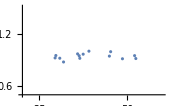
```mathematica
Cases[-Graphics-,Point[{x__}]->x,Infinity]
```

{{31.897,0.877048},{29.4908,0.923083},{48.6565,0.913594},{52.4657,0.916115},{29.7093,0.950648},{44.9433,0.943592},{36.5236,0.918793},{39.1192,0.999671},{37.4837,0.965564},{52.1153,0.949088},{36.3386,0.947845},{35.8976,0.969093},{45.2999,0.993827},{30.8256,0.919682}}

In general:

```mathematica
Cases[plot,x_GraphicsType:>First@x,Infinity]//First;
```

E.g.

```mathematica
Cases[-Graphics-,x_Point:>First@x,Infinity]
```

{{{31.897,0.877048},{29.4908,0.923083},{48.6565,0.913594},{52.4657,0.916115},{29.7093,0.950648},{44.9433,0.943592},{36.5236,0.918793},{39.1192,0.999671},{37.4837,0.965564},{52.1153,0.949088},{36.3386,0.947845},{35.8976,0.969093},{45.2999,0.993827},{30.8256,0.919682}}}

Extract options such as frame tick positions:

```mathematica
Options[BarChart[{1,2,3}],FrameTicks]
```

{FrameTicks→{{Automatic,Automatic},{{{1.,,{0.004,0}},{2.,,{0.004,0}},{3.,,{0.004,0}}},{{1.,,{0.004,0}},{2.,,{0.004,0}},{3.,,{0.004,0}}}}}}

## Beyond basic plotting (additional features)

Use Show to reformat plots or combine different plots. Use Overlay to overlay plots.

Legends for complicated/combined plots:

Graphs with legends consists of two parts, graph and legends:

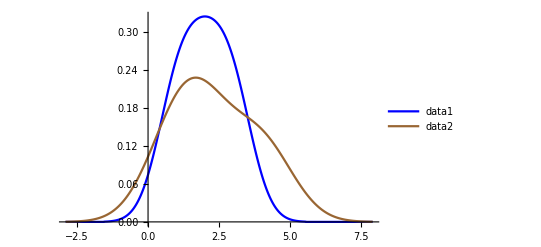

```mathematica
samplePlot=SmoothHistogram[{{1,3,2},{2,4,1}},PlotLegends->{"data1","data2"},PlotStyle->{Blue,Brown}]
```

```mathematica
samplePlot[[2]]
```

Placed[,After,Identity]

Use legending functions (LineLegend, SwatchLegend, BarLegend...) to construct legends:

```mathematica
lgnds=LineLegend[{Directive[AbsoluteThickness[1.6], RGBColor[0, 0, 1]], 
  Directive[AbsoluteThickness[1.6], RGBColor[0.6, 0.4, 0.2]]}, {"data1", "data2"}, LabelStyle->Orange,LegendLayout->"Column"]
```

Use Legended to construct a legend for a graphic:

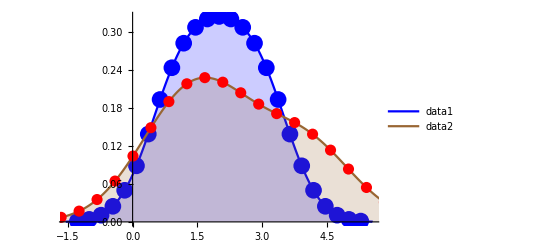

```mathematica
plot=Show[SmoothHistogram[{1,3,2},Filling->Axis,Mesh->25,MeshStyle->Directive[PointSize[0.03],Blue],PlotStyle->Blue],SmoothHistogram[{2,4,1},Filling->Axis,Mesh->25,MeshStyle->Directive[PointSize[0.02],Red],PlotStyle->Brown]];
Legended[plot,lgnds] (* or plot~Legended~samplePlot[[2]] *)
```

Customize the appearance of the legend:

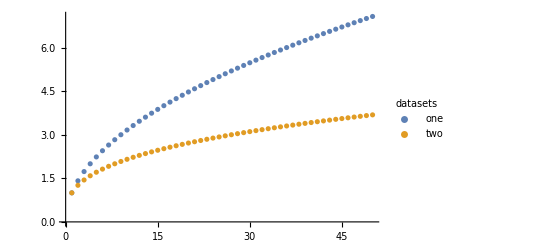

```mathematica
ListPlot[{√Range[50],Range[50]^(1/3)},PlotLegends->PointLegend[Automatic,{"one","two"},LegendFunction->"Frame",LegendLabel->"datasets"]]
```

Creation of customized graphics. (need improvements, need to find good applications)

```mathematica
Graphics[{White,EdgeForm[Directive[Thick,Blue]],Disk[]}]
```

```mathematica
Column[{Legended[Graphics[{Blue,Thick,Line[{{-0.5,0},{0.5,0}}],Green,EdgeForm[Directive[Thick,Blue]],Disk[{0,0},0.25],Black},ImageSize->35],Style["legend 1",25,FontFamily->"Helvetica"]],
Legended[Graphics[{Red,Thick,Line[{{-0.5,0},{0.5,0}}],Yellow,EdgeForm[Directive[Thick,Red]],Disk[{0,0},0.25],Black},ImageSize->35],Style["legend 2",25,FontFamily->"Times New Roman"]],Legended[Graphics[{Blue,Thick,Line[{{0,0.5},{1,0.5}}],Blue,EdgeForm[Directive[Thick,Blue]],Rectangle[{0.3,0.3},{0.7,0.7}],Black},ImageSize->35],Style["legend 3",25,FontFamily->"Arial"]]}]
```

-Graphics-
-Graphics-
-Graphics-

Use function Show or option Epilog to include graphics within the plotting region of the plot (as legend or comments, for example). 

Automatic generation of legend by including graphics as markers is also viable (just less control over the graphics):

```mathematica
LineLegend[{Red,Green,Blue},{"label1","label2","label3"},LegendMarkers->{Graphics[Disk[]],Graphics[Rectangle[]],Graphics[Circle[]]}]
```

Color the plot using ColorFunction:

```mathematica
Plot[Sinc[x],{x,0,10},PlotStyle->Thick,ColorFunction->Function[{x,y},ColorData["NeonColors"][y]]]
```

To use x value as coloring input function, use:

```mathematica
ColorFunction->Function[{x,y},ColorData["NeonColors"][x]]
```

Customize frame ticks

```mathematica
FrameTicks->{{Automatic,None},{{Range[xMin,xMax,xStep],Ceiling/@(Range[xMin,xMax,xStep]*100)}ᵀ,None}}
(*this shows ticks at specific tick positions with tick labels scaled*)
```

## Customized functions

Generate plots with Two different Scales

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

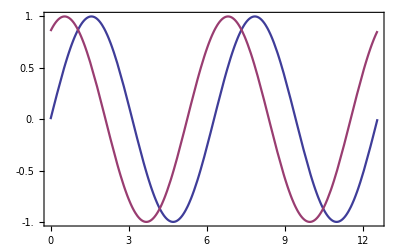

```mathematica
TwoAxisPlot[{Sin[x],3 Sin[x]+5 Cos[x]},{x,0,4 Pi}]
```

```mathematica
TwoAxisListPlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListPlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

(*variant*)
TwoAxisListPlot[{list1_,list2_},opts:OptionsPattern[]]:=Module[{plot1,plot2,ranges},{plot1,plot2}=ListLinePlot/@{list1,list2};
ranges=Last@Charting`get2DPlotRange@#&/@{plot1,plot2};
ListPlot[{list1,Rescale[list2,Last@ranges,First@ranges]},Frame->True,FrameTicks->{{Automatic,Charting`FindTicks[First@ranges,Last@ranges]},{Automatic,Automatic}},FrameStyle->{{Automatic,ColorData[97][2]},{Automatic,Automatic}},FilterRules[{opts},Options[ListPlot]]]]

TwoAxisListLinePlot[{f_,g_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=Last[PlotRange/.AbsoluteOptions[#,PlotRange]]&/@{fgraph,ggraph};
fticks=Last[Ticks/.AbsoluteOptions[fgraph,Ticks]]/._RGBColor|_GrayLevel|_Hue:>ColorData[1][1];
gticks=(MapAt[Function[r,Rescale[r,grange,frange]],#,{1}]&/@Last[Ticks/.AbsoluteOptions[ggraph,Ticks]])/._RGBColor|_GrayLevel|_Hue->ColorData[1][2];
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Transparent}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

Test:

```mathematica
d1=Accumulate[RandomReal[{0,1},{100}]];
d2=Accumulate[RandomReal[{0,50},{100}]];
{{ListLinePlot[d1],ListPlot[d2]},{TwoAxisListPlot[{d1,d2}],TwoAxisListPlot[{d1,d2},Joined->True],TwoAxisListLinePlot[{d1,d2}]}}
```

Categorical scatter plot

```mathematica
catListPlot[x_,o:OptionsPattern[]]:=Block[{c},c=Transpose[{#,Range[Length[#]]}]&[DeleteDuplicates[x[[All,1]]]];
ListPlot[x/.(Rule@@@c),Ticks->{MapAt[Rotate[#,90Degree]&,2]/@Reverse/@c,Automatic},o]]
```

## Tables of figures

Use Grid or GraphicsGrid
sometimes Grid gives issues with sizes and alignment during export, in this case use GraphicsGrid to freeze the entire table. 
Use spacings to adjust space between figures.

```mathematica
GraphicsGrid[{{plot1,plot2}},Spacings->{Scaled[-.16],Scaled[-.1]},ImageSize->850]
```

## Useful plotting options

For SERIS style, use frames instead of axes. 
Able to support arbitrary tick labels (other than numbers) using FrameTicks. 
Note not all options listed below can coexist.

```mathematica
plottingFunction[data,
PlotRange-> {{0.1,1.3},{0,0.2}},
PlotRangeClipping->True,
PlotRangePadding->{{None,Scaled[.03]},None},
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Black,Thickness[0.003]],
FrameLabel->{"x","y"},
FrameTicks->{{Automatic,None},{{{1,"tick a"},{10,"tick b"},{20,"tick c"}},None}},
(* FrameTicks and FrameLabel format is {{Left y, right y},{bottom x, top x}} *)
BaseStyle->Directive[15,Bold],
Joined->False,
PlotMarkers->-Graphics3D-,
GridLines->{None,{{1,Dashed}}},
AspectRatio->1/10,
PlotStyle->Directive[Dashed,Red],(*or something like PointSize[0.02]*)
ImageSize->Large,ImageMargins->15,
TicksStyle->Directive[Orange,12],
Mesh->Full,
MeshStyle->Directive[Red,PointSize[0.03]]]
(* Mesh->All seem to be unable to distinguish between different series of plots, use Full instead and it sometimes can work *)
```

Take note of format differences for the relative positions for function Placed:

```mathematica
ChartLegends->Placed[{"legend 1","legend 2"},{{0.8,0.6}}]
ChartLabels->Placed["title",{0.8,0.95}]
```

Set default options for plot functions:

```mathematica
SetOptions[ListPlot,
Frame->True,
Axes->False,
LabelStyle->{FontFamily->"Helvetica",FontSize->22,FontWeight->Bold,FontColor->Black},
FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.0025]],
ImageSize->Large,ImageMargins->15];
```

```mathematica
plotOptions={Frame->{{True,True},{True,True}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Directive[Black,Thickness[0.003]],LabelStyle->{FontFamily->"Helvetica",FontSize->15,FontWeight->Bold,FontColor->Black}};
```

GeoLabels
slot #1 is the graphics object, #2 refers to object name, #3 is geo coordinates, #4 is value.

```mathematica
GeoLabels->(Tooltip[#1,#2[[2]]<>" : "<>ToString@#4]&)
```

## Examples and cases

## Wind rose diagram

```mathematica
binwidth=360/30;
dataRange=10;
dataStep=2;
With[{data=fullData["[134]OnSMet"][All,"AvgWindD_OnS"]//Normal},
SectorChart[Thread[{ConstantArray[1,360/binwidth],BinCounts[data,{0,360,binwidth}]/Length[data]*100//N}],BaseStyle->{15,Bold},SectorOrigin->{Pi/2,"Clockwise"},PolarAxes->True,PolarGridLines->Automatic,PolarAxesOrigin->{0.5 Pi,dataRange+dataStep},PolarTicks->{"Direction",Thread[{Range[0,dataRange,dataStep],ToString[#]<>"%"&/@Range[0,dataRange,dataStep]}]},ChartBaseStyle->Directive[Opacity[1],EdgeForm[Thin]],PlotLabel->"On Shore"]]
```

-Graphics-

## List plot

### Plot with legends and labels

For use in publications, reports...

```mathematica
DateListPlot[diff,
Frame->True,FrameStyle->Directive[Black,Thickness[0.0025]],FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{None,"temperature difference (°C)"},
Axes->False,
PlotStyle->Blue,
PlotMarkers->{Graphics[{Green,EdgeForm[Directive[Thick,Blue]],Disk[]}],0.03},
LabelStyle->{FontFamily->"Helvetica",FontSize->28,FontWeight->Bold,FontColor->Black},
PlotLegends->Placed[Legended[Graphics[{Blue,Thick,Line[{{-0.5,0},{0.5,0}}],Green,EdgeForm[Directive[Thick,Blue]],Disk[{0,0},0.25],Black},ImageSize->35],Style["legend 1",30,FontFamily->"Helvetica"]],{0.8,0.9}],
Epilog->Text[Style["(a)",28,Bold],Scaled[{0.05,0.9}],{-1,0}],
ImageSize->600,ImageMargins->15,AspectRatio->1/1.3]
```

-Graphics-

### ListPlot with text as x-labels?

## Date List Plot

Use DateTickFormat to change the labeling of time stamps.

```mathematica
DateTicksFormat->{"MonthNameShort"," ","YearShort"}
```

## Bars and distribution plots

Bar chart plot ranges go from 0.5 to length of data + 0.5.

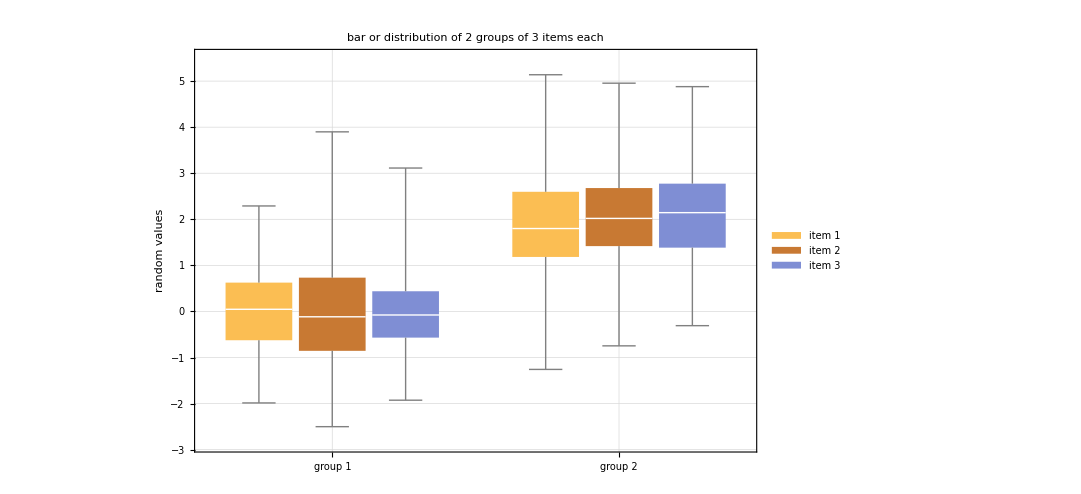

```mathematica
BoxWhiskerChart[Table[RandomVariate[NormalDistribution[μ,1],100],{μ,{0,2}},{3}],ChartLabels->{(Rotate[#,25Degree]&/@{"group 1","group 2"}),None},ChartLegends->{"item 1","item 2","item 3"},TicksStyle->Directive[18, Bold,Black],GridLines->Automatic,BarSpacing->{0.1,1},(*use BarSpacing to adjust spacing within and between groups *)
Frame->True,FrameStyle->Directive[Black,Thickness[0.0025]],FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{None,Style["random values",28,Bold,Black]},LabelStyle->{FontFamily->"Helvetica",FontSize->22,FontWeight->Bold,FontColor->Black},ImageSize->Medium,PlotLabel->"bar or distribution of 2 groups of 3 items each"]
```

## Mixed type plots

### Bar chart with list plots

(Example from Mathematica Stack Exchange)

```mathematica
purple=RGBColor[97/255,16/255,106/255];
orange=RGBColor[245/255,132/255,31/255];
labels={"FY15 Q1/2","FY15 Q3/4","FY16 Q1/2","FY16 Q3/4","FY17 Q1/Q2","FY17 Q3/Q4","FY18 Q1/2","FY18 Q3/4"};
starvedTime={7.55,11.23,8.58333,6.88833,4.65167,1.89,6.49833,1.95};
satTime={70.1483,81.1467,81.115,86.5483,84.6833,90.685,79.6017,91.0133};
```

#### Method 1

Plot two graphs separately, then overlay them. Make sure the alignment by carefully controlling the graphing elements.

```mathematica
box=Graphics[{purple,Rectangle[]},ImageSize->12];
text="Smelter Starved (%)";
line=Graphics[{orange,Line[{{0,0.5},{1,0.5}}]},ImageSize->{30,Automatic}];
text2="% Time Smelter at Constraint Rate (%)";
legend=Grid[{{box,text,line,text2}},Alignment->{{Right,Left},Center},BaseStyle->Directive[FontFamily->"Arial"],Spacings->{{0,0.5,2},0}];
```

```mathematica
plot1=BarChart[starvedTime,AspectRatio->1/GoldenRatio,AxesOrigin->{0,0},BarSpacing->1,BaseStyle->Directive[FontFamily->"Arial"],ChartLabels->Placed[labels,Below],ChartStyle->purple,Frame->{True,True,True,False},FrameLabel->{None,"Smelter Starved Time (%)",None,None},FrameTicks->{{#,"",{0,0.01}}&/@Range[0.5,8.5,1],{0,3,6,9,12},None,None},FrameTicksStyle->Directive[Plain,12],GridLines->{None,{3,6,9}},GridLinesStyle->Directive[Gray,Dashed],ImagePadding->{{50,50},{20,10}},ImageSize->600,LabelStyle->Directive[Bold,12],PlotLabel->Style["Smelter Starved Time by 6 Month Period: Base Case",13],PlotRange->{{0.5,8.5},{0,12}},PlotRangePadding->0,Ticks->None];

plot2=ListPlot[satTime,AspectRatio->1/GoldenRatio,Axes->False,Mesh->All,BaseStyle->Directive[FontFamily->"Arial"],DataRange->{1,8},Frame->{False,False,False,True},FrameTicks->{None,None,None,{60,70,80,90,100}},FrameTicksStyle->Directive[Plain,12],FrameLabel->{None,None,None,"Smelter Operating at Constraint Rate (%)"},ImageSize->600,ImagePadding->{{50,50},{20,10}},Joined->True,LabelStyle->Directive[Bold,12],PlotRangePadding->0,PlotRange->{{0.5,8.5},{60,100}},PlotStyle->orange,PlotLabel->Style["",13]];
```

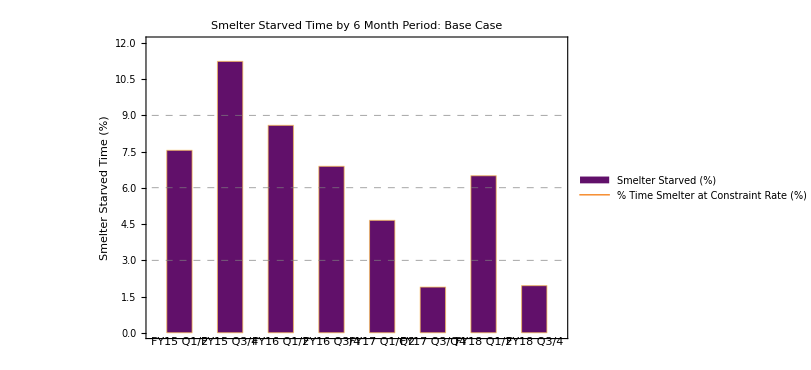
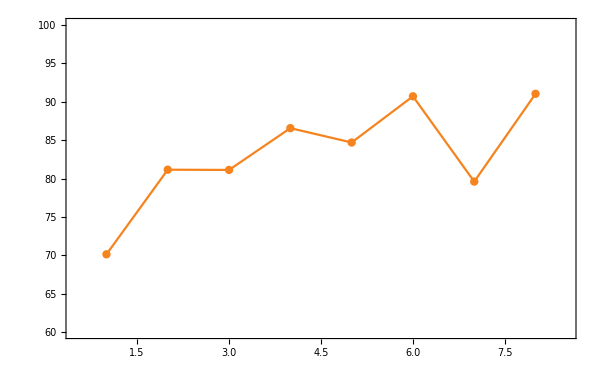

```mathematica
Legended[Overlay[{plot1,plot2}],Placed[legend,Below]]
```

#### Method 2

Directly construct graphics.

First some prepared parts:

```mathematica
lblspec=Join[MapIndexed[{#2[[1]],#,0}&,labels],{#,"",{0,0.01}}&/@Range[1.5,8,1]];

box=Graphics[{purple,Rectangle[{0,0},{2.7,1}]},ImageSize->27];
text="Smelter Starved (%)";
text2="% Time Smelter at Constraint Rate (%)";
line=Graphics[{orange,Line[{{0,0.5},{1,0.5}}]},ImageSize->30];
legend=Row@{box,Spacer[5],text,Spacer[50],line,Spacer[5],text2};
```

Then auxiliary functions and a style definition:

```mathematica
style1={FontFamily->"Tahoma",11};

bar[w_][h_,{p_}]:=Rectangle[{p-w/2,0},{p+w/2,h}] (*width,height,position*)

scale=Rescale[#,{60,100},{0,12}]&;(*range of each y axis*)
```

Finally, the graphics:

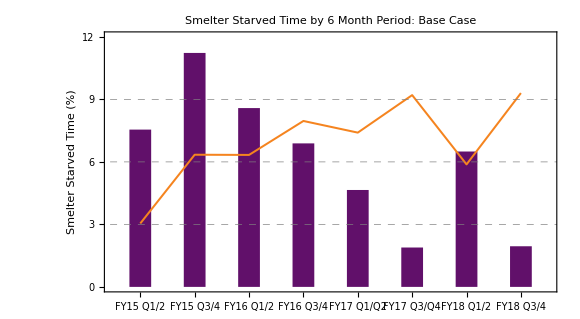
-Graphics-
-Graphics-Smelter Starved (%)-Graphics-% Time Smelter at Constraint Rate (%)

```mathematica
Graphics[{{purple,bar[0.4]~MapIndexed~starvedTime},{orange,Thickness[0.0025],Line[{#2[[1]],scale@#}&~MapIndexed~satTime]}},PlotRange->{{0.5,8.5},{0,12}},GridLines->{None,{3,6,9}},GridLinesStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{{Range[0,12,3],{scale@#,#}&/@Range[60,100,10]},{lblspec,None}},LabelStyle->style1,FrameLabel->{None,Style["Smelter Starved Time (%)",Bold],Spacer[{0,10}],Style["Smelter Operating at Constraint Rate (%)",Bold]},PlotLabel->Style["Smelter Starved Time by 6 Month Period: Base Case",FontFamily->"Helvetica",Bold,14],ImageSize->580,AspectRatio->0.55]//Grid[List/@{#,legend~Style~style1}]&
```

#### Method 3

BarChart with Epilogs

#### Method 4

ListPlot with Prologs

## Geographic visualization

### Overlay a density plot on a geographic map background

```mathematica
t=QuantityMagnitude[GeomagneticModelData[{{-90,-180.},{90,180.}},"Magnitude",GeoZoomLevel->-2]];

data=t;
plot=ListDensityPlot[data,PlotRangePadding->0,ColorFunction->"TemperatureMap",Frame->False,InterpolationOrder->2,ImageSize->Medium]
GeoGraphics[{GeoStyling[{"GeoImage",plot},GeoRange->{{-90,90},{-180,180}}],Opacity[0.7],GeoBoundsRegion["World"]},GeoRange->"World",GeoProjection->"WinkelTripel",GeoBackground->{"Coastlines","Land"->White,"Ocean"->White,"Border"->Black}]
```

-Graphics-

-Graphics-

To clip and only show values on land areas, use Polygon to create a mask:

```mathematica
geoPlot=GeoGraphics[{GeoStyling[{"GeoImage",plot},GeoRange->{{-90,90},{-180,180}}],CountryData["World","Polygon"]},GeoRange->{{-60,88},{-179,180}},GeoProjection->"Robinson",GeoBackground->{"Coastlines","Land"->White,"Ocean"->LightBlue,"Border"->Black},ImageSize->600]
```

-Graphics-

Create mask of country borders:

```mathematica
mask=ColorReplace[GeoGraphics["World",GeoBackground->GeoStyling["CountryBorders"],GeoProjection->"Robinson",GeoRange->{{-60,88},{-179,180}},ImageSize->1200],{RGBColor[0.9992163476681813, 0.9327206156201098, 0.8191704451348238]->White,RGBColor[0.6193818061412687, 0.6180822774785095, 0.6153791313536497]->Black}]
```

-Graphics-

```mathematica
Show[ImageResize[geoPlot,{180*5,90*5}],ImageResize[ColorReplace[mask,White->Transparent],{180*5,90*5}]]
(* cannot directly create a mask by replacing color to transparent for some reason, so replace color again here. ImageResize is somehow needed, as these graphics cannot directly combine *)
```

-Graphics-

### Useful function

```mathematica
toGeoGraphics[Shortest[opac:_?NumericQ:0.6],opts:OptionsPattern[GeoGraphics]][in_]:=With[{trans=If[MatchQ[OptionValue[GeoProjection],Automatic|"Equirectangular"],{},gc_GraphicsComplex:>MapAt[GeoPosition@*Map[Reverse],gc,1]]},in/.Graphics[prim_,___]:>GeoGraphics[{Opacity@opac,prim/.trans},opts,Options@toGeoGraphics]]
```

```mathematica
Options[toGeoGraphics]={GeoBackground->GeoStyling["StreetMapNoLabels"],ImageSize->600};
```

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-180,180},{y,-90,90},PlotLegends->Automatic]//toGeoGraphics[GeoProjection->"Mollweide"]
```

## Correlation table plots

```mathematica
mem=CountryData["G7"];
cdata=(QuantityMagnitude/@CountryData[#,{"InflationRate",{2000,2010}}]["Values"]&)/@mem;
```

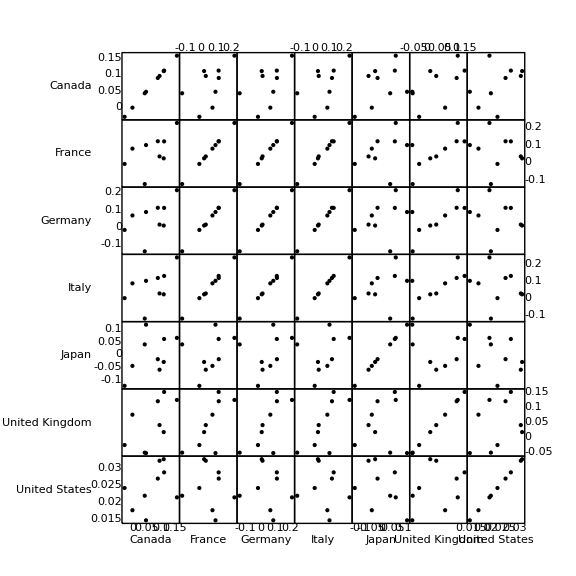

```mathematica
ResourceFunction["PairwiseScatterPlot"][Transpose@cdata,"DataTicks"->True,ImageSize->Large,"DataLabels"->mem]
```

```mathematica
fnCorrelationTablePlot[variables_,data_]:=Module[{cmatrix=Correlation@data,imageSize=400},
Column[{GraphicsRow[variables,ImageSize->imageSize,Frame->All],Row[{GraphicsColumn[variables,ImageSize->{imageSize/Length@variables,imageSize},Frame->All],Overlay[{ArrayPlot[cmatrix,ColorFunction->(ColorData["TemperatureMap"][(1+#)/2]&),Frame->None,Mesh->True,PlotRangePadding->0,ImageSize->{imageSize,imageSize},ColorFunctionScaling->False],GraphicsGrid[Map[NumberForm[#,2]&,cmatrix,{2}],ImageSize->{imageSize,imageSize}]}]}]},Alignment->Right,Spacings->0]];
```

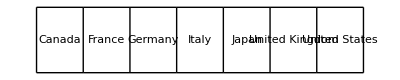
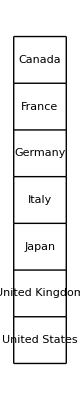
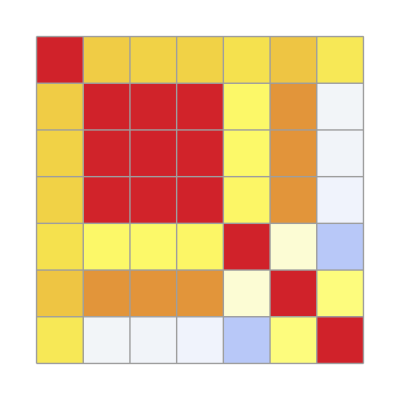
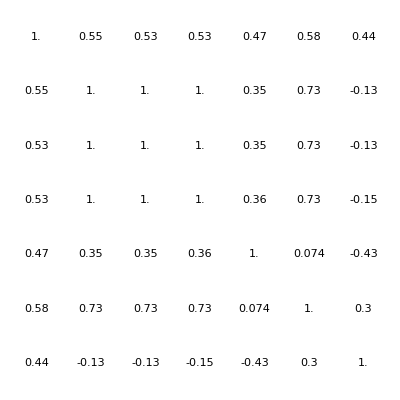

```mathematica
fnCorrelationTablePlot[mem,Transpose@cdata]
```

## Exporting plots

Export .tiff figure for common academic publishing with required DPI of 300. (ImageResolution is not an option in plotting, only for exporting)

```mathematica
Export["figure.tiff",plot,ImageResolution->300,"ImageEncoding"-> "LZW"]
```

When plot format shifts during export, use Rasterize to convert to pixel image to fix the display format.

```mathematica
Rasterize[plot,RasterSize->1500]
```

Export animation of a list of plots with speed control:

```mathematica
Export["animation.gif",Table[Plot[Sin[a+x],{x,0,10}],{a,0,10}],"DisplayDurations"->1]
```

## Tables

creating simple tables

```mathematica
Grid[table,ItemSize->All,Frame->All]
```